# Map Exercises

## Basic Exercises

### Question Subsection

We will use the separate function again. We vectorized this function using Table as follows:

```mathematica
separate[a_Integer?Positive]:=Framed[a,Background->LightRed]
separate[a_Integer?Negative]:=Framed[a,Background->LightBlue]
separate[a_Real]:=Framed[a,Background->Yellow]
separate[x_List]:=Table[separate[n],{n,x}](*Change this line*)
```

Vectorize it using Map instead.

#### Solution

```mathematica
separate[a_Integer?Positive]:=Framed[a,Background->LightRed]
separate[a_Integer?Negative]:=Framed[a,Background->LightBlue]
separate[a_Real]:=Framed[a,Background->Yellow]
separate[x_List]:=separate/@x
```

```mathematica
separate[{-2,3,2.2,5.4,-3,5,-3.3}]
```

{-2,3,2.2,5.4,-3,5,-3.3}

## Intermediate Exercises

### Question Subsection

Write a function that takes a list of numbers and raises them to the power of the position the numbers are at.

```mathematica
list =Table[RandomInteger[10],10]
```

{6,5,5,9,3,7,6,7,4,3}

#### Hints

You might find the function MapIndexed useful.

#### Solution

```mathematica
power[a_,b_]:=a^b[[1]]
```

```mathematica
MapIndexed[power,list]
```

{6,25,125,6561,243,117649,279936,5764801,262144,59049}

### Question Subsection

Write a function that squares and highlights the values in a list only at specific positions of {2,6,7}.

```mathematica
list =Table[RandomInteger[10],10]
```

{6,3,0,9,2,2,10,5,4,10}

#### Hints

Take a look at the function MapAt.

#### Solution

```mathematica
squareHighLight[x_]:=Framed[x^2,Background->Yellow]
```

```mathematica
MapAt[squareHighLight,list,{{2},{6},{7}}]
```

{6,9,0,9,2,4,100,5,4,10}

### Question Subsection

Write a function that finds the inner product of two vectors.

```mathematica
v1={4,5,2,6,7};
v2={6,3,7,2,2};
```

#### Hints

Assume vectors are given in the form of lists.

Inner product of two vectors {a,b,c} and {A,B,C} is aA+bB+cC.

Checkout the function MapThread.

#### Solution

```mathematica
Total[MapThread[Times,{v1,v2}]]
```

79

## Advanced Exercises

### Question Subsection

Make use of pattern testing, function definition, and Map to write a program that takes a list of pairs of numbers {x,y} between 0 and 1, and categorizes them along the lines of x=0.5 and y=0.3. Write the function so that it returns list of objects ready to be plotted using Graphics, but each category should have a different color. Plot these points.

```mathematica
points = Table[{RandomReal[],RandomReal[]},1000];
```

#### Hint

This is very similar to the separate function we wrote earlier.

#### Solution

```mathematica
categorize[{x_/;x>0.5,y_/;y>0.3}]:={PointSize@Large,Red,Point[{x,y}]}
categorize[{x_/;x>0.5,y_/;y≤0.3}]:={PointSize@Large,Blue,Point[{x,y}]}
categorize[{x_/;x<=0.5,y_/;y>0.3}]:={PointSize@Large,Green,Point[{x,y}]}
categorize[{x_/;x<=0.5,y_/;y<=0.3}]:={PointSize@Large,Yellow,Point[{x,y}]}
categorize[l:{___List}]:=Map[categorize,l]
```

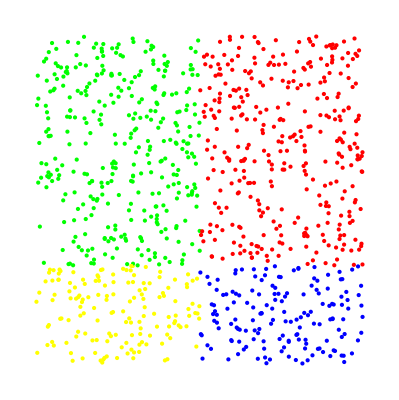

```mathematica
Graphics[categorize[points]]
```

### Question Subsection

Rewrite the same program above, but this time, vary the shade of the color of each category based on the coordinates of the points. In addition, use MapIndexed and pattern matching to plot the points that are in the following specified positions in the list in black.

```mathematica
positions=Table[RandomInteger[Length[points]],100];
```

#### Hint

You might find the function MemberQ useful.

#### Solution

```mathematica
categorizeGradient[{x_/;x>0.5,y_/;y>0.3}]:={PointSize@Large,RGBColor[1,x,y],Point[{x,y}]}
categorizeGradient[{x_/;x>0.5,y_/;y≤0.3}]:={PointSize@Large,RGBColor[x,y,1],Point[{x,y}]}
categorizeGradient[{x_/;x<=0.5,y_/;y>0.3}]:={PointSize@Large,RGBColor[x,1,y],Point[{x,y}]}
categorizeGradient[{x_/;x<=0.5,y_/;y<=0.3}]:={PointSize@Large,RGBColor[0.9,0.9,0.5+(x+y)/2],Point[{x,y}]}
```

```mathematica
categorizeGradient[{x_,y_},"Special"]:={PointSize[.02],Black,Point[{x,y}]}
```

```mathematica
categorizeGradient[{x_,y_},index_/;MemberQ[positions,index[[1]]]]:=categorizeGradient[{x,y},"Special"]
categorizeGradient[{x_,y_},index_]:=categorizeGradient[{x,y}]
```

```mathematica
categorizeGradient[l:{___List}]:=MapIndexed[categorizeGradient,l]
```

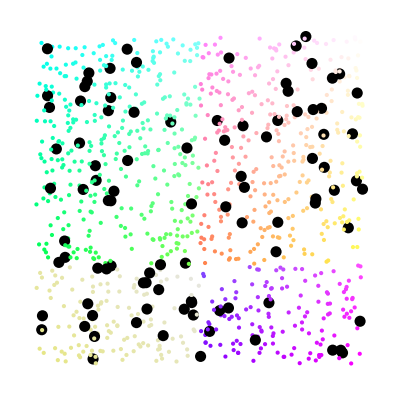

```mathematica
Graphics[categorizeGradient[points]]
```